# Leak Current

## Parameters

```mathematica
(*parameters*)lParameters={gl->0.1,el->-50,cm->1700(*unit conversions*)};
```

## Differential Equations

```mathematica
(*there are no steady-state equations because it is voltage-independent*)(*differential equations*)membrane=NDSolve[{cm*V'[t]==-gl*(V[t]-el),V[0]==-40}/.lParameters,V[t],{t,0,30}];
```

## Plots

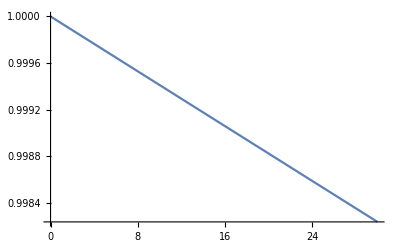

```mathematica
Plot[Evaluate[gl*(V[t]-el)/.membrane[[1,All]]/.lParameters],{t,0,30}]
```